```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\DK\OneDrive - Duke University\_Doc\repositories\fishbonett\examples

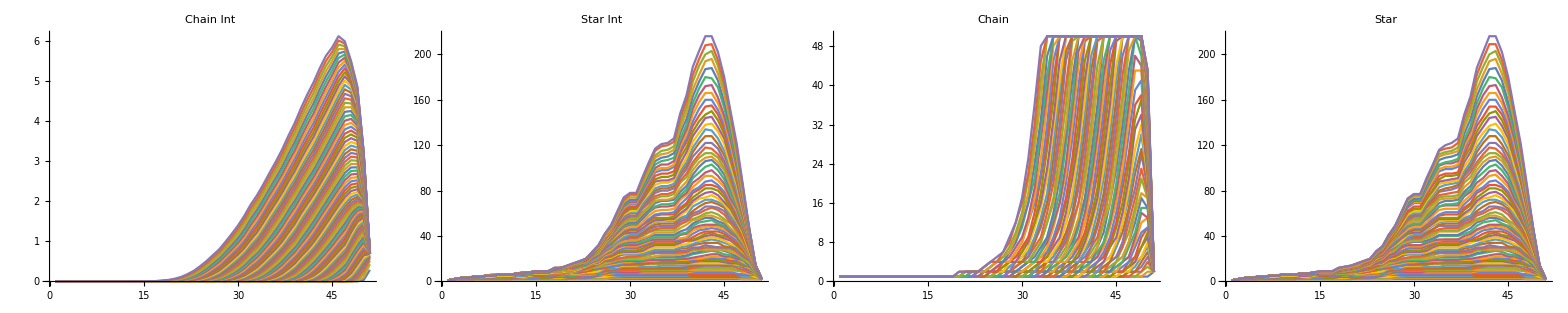

```mathematica
data1=ArrayReshape[#,{80,51}]&[BinaryReadList["heatmap.dat","Real32"]];data2=ArrayReshape[#,{80,51}]&[BinaryReadList["heatmap_star1.dat","Real32"]];data3=ArrayReshape[#,{80,51}]&[BinaryReadList["heatmap_chain.dat","Real32"]];data4=ArrayReshape[#,{80,51}]&[BinaryReadList["heatmap_star_int.dat","Real32"]];
llpset={ColorFunction-> "SouthwestColors"};
Grid[{
{ListLinePlot[data1,PlotRange->All,PlotLabel->"Chain Int"],
ListLinePlot[data4,PlotRange->All,PlotLabel->"Star Int"],
ListLinePlot[data3,PlotRange->All,PlotLabel->"Chain"],
ListLinePlot[data2,PlotRange->All,PlotLabel->"Star"]
}}
]
```

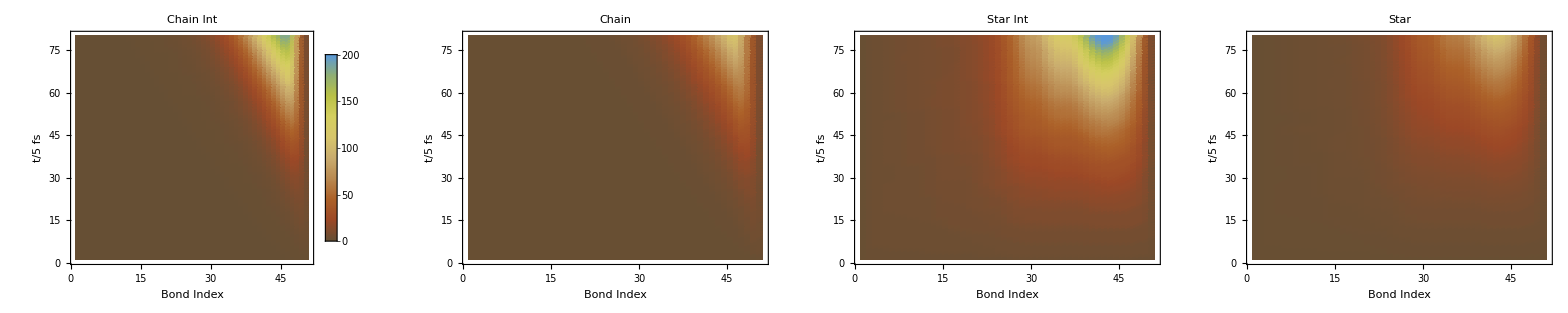

```mathematica
ldpset={PlotRange->Full,ColorFunctionScaling->False,ColorFunction->"SouthwestColors",LabelStyle->{FontFamily->"DejaVu Sans",13},FrameLabel->{"Bond  Index","t/5 fs"}};Legended[#,BarLegend[{"SouthwestColors",{0,200}},LegendMarkerSize->120]]&[Grid[{
{ListDensityPlot[data1/400,ldpset,PlotLabel->"Chain  Int"],
ListDensityPlot[data3/200,ldpset,PlotLabel->"Chain"],
ListDensityPlot[data4/200,ldpset,PlotLabel->"Star  Int"],
ListDensityPlot[data2/400,ldpset,PlotLabel->"Star"]
}},ItemSize->15,Spacings->{0, 0}
]
]
```

```mathematica
(*spectral density*)gam=100/1.8;drude=2* (100/Pi)*gam(x/(x^2+gam^2));

(*weight function is the square of ψ*)
w=drude;

(*norm of the weight function*)
normw=1;

(*normalized weight function*)
wnormed=w/normw;

(*orthogonalizes the monomials 1,x,x^2,x^3,...,x^n assuming an inner-product convolution with normalized weight fn*)
symbasis[n_?IntegerQ]:=Orthogonalize[x^#&/@Range[0,n],Integrate[wnormed*#1*#2,{x,0,350}]&]
```

```mathematica
k=Simplify[symbasis[7]]
```

{0.0123526,0.000133955 (-146.508+x),0.0297571-0.000515589 x+1.52766×10^-6 x^2,-0.0415107+0.00126689 x-9.04628×10^-6 x^2+1.7492×10^-8 x^3,0.0546085-0.00253474 x+0.000031369 x^2-1.39162×10^-7 x^3+2.00339×10^-10 x^4,-0.0689017+0.00448317 x-0.0000833972 x^2+6.23031×10^-7 x^3-1.99844×10^-9 x^4+2.29389×10^-12 x^5,0.0842886-0.00729112 x+0.000188055 x^2-2.07128×10^-6 x^3+1.09593×10^-8 x^4-2.74987×10^-11 x^5+2.6257×10^-14 x^6,-0.100692+0.0111512 x-0.000378398 x^2+5.69624×10^-6 x^3-4.37533×10^-8 x^4+1.78443×10^-10 x^5-3.67506×10^-13 x^6+3.00472×10^-16 x^7}

```mathematica
Plot[Table[Re[NIntegrate[k[[i]]* Cos[x t],{x,0,350}]],{i,1,7}],{t,0,0.2},PlotRange->Full,PlotLegends->Automatic]
```

$Aborted

```mathematica
NIntegrate[{x^2,x^3}* Cos[x ],{x,0,350}]
```

{-117666.,-4.12165×10^7}

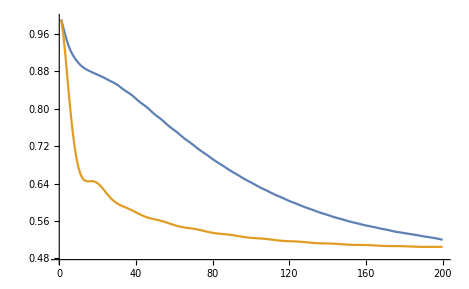

```mathematica
ListLinePlot[{{0.9914819396215323,0.9754342235582868,0.9596458005218373,0.9454795955791108,0.9334056772779362,0.9235055479574436,0.9154778835037916,0.9088419588063488,0.903156783996445,0.8981646756057842,0.893815203386728,0.8901433535265935,0.8871133725556154,0.8845813254176639,0.8823685355833557,0.8803313112073401,0.8783812769739833,0.8764842538005192,0.874641213575078,0.8728439502904962,0.8710489404688928,0.8692015100871706,0.8672583695104877,0.8651891753874265,0.8630186727620671,0.8608425937630106,0.8587283650202384,0.856646522811546,0.8544973347862008,0.8521104194648238,0.8493136791530194,0.8461425609528468,0.8428926506177321,0.8398689009337345,0.8371377154522355,0.8345467307341851,0.8318634134311735,0.8288643824742715,0.8254458464475528,0.8217392951392763,0.8180542572633507,0.8146491295200908,0.8115607490702755,0.8086227179894361,0.8055984859758363,0.8022823788805944,0.7986177273285431,0.7947626817328672,0.7910014840273504,0.7875427357254706,0.7843816483605761,0.7813620646401261,0.7782456443257721,0.7748715803762699,0.7712166546254356,0.7674555708481937,0.7638257531110056,0.760478723511305,0.7573844744088709,0.754397692275983,0.751314367763803,0.7480152256249447,0.7445148468671569,0.7409757270028424,0.7375714988942029,0.7344230501260282,0.7314747916016763,0.728611840765168,0.7256462808831824,0.7225061203524176,0.719227945385013,0.7159447006941642,0.712792211591445,0.7098580947439597,0.7070995787669069,0.7043868724824668,0.7015991786578386,0.6986493061471576,0.695598446744054,0.6925762460143249,0.6896960018908667,0.686999810940551,0.6844736171483271,0.6819728731700829,0.6793696311125966,0.6766510478490767,0.6738527299263796,0.6710972879120921,0.6684794049623186,0.6660363721403186,0.6637227866681641,0.6613945081409632,0.6590001306597013,0.6565036781253459,0.6539524001057488,0.6514581443757352,0.6491088875928274,0.6468978569298466,0.6447785149727618,0.6426777630524492,0.6404624925005225,0.6382043657301006,0.6358831407631613,0.6336379749389343,0.6315087039172145,0.6295395959981438,0.6276371786735239,0.6257216691736227,0.6237159388955825,0.621614437754362,0.6195091213292189,0.6174955956128225,0.6156283009370663,0.6138810423813774,0.6121818500493998,0.6104500704505683,0.6086541454143046,0.6067560228320538,0.6048447969157738,0.6030226834008471,0.6013452407981558,0.5997735537042846,0.5982368551383834,0.5966461868340032,0.5950041454626707,0.5933080594148745,0.5916055627583354,0.5900023650839072,0.5885052142495434,0.5871026741092737,0.585717233988543,0.584280540906851,0.5827480768885704,0.5812148894868697,0.5796871287450817,0.5782289647002209,0.5769109313856763,0.5756768911557667,0.5744446252253276,0.5731365814814673,0.5717842986869575,0.5703872409270522,0.5690396060059538,0.5677575607845314,0.5666292008401681,0.5655229588013666,0.5644439758243309,0.5632766426101014,0.562038875094503,0.5608106229320811,0.5595785610298633,0.5585060536970673,0.5575427190447123,0.5565775233010797,0.5556436216435818,0.5546388755999103,0.5536025053529797,0.552557057461571,0.5515317468708438,0.5506207287675454,0.5497912272844214,0.5490191654422755,0.5482286152736815,0.5473802551257106,0.546459176362499,0.5455334471283284,0.5446248204641141,0.5437327563556084,0.5429850226400958,0.5421870397846753,0.5413742568341473,0.5404740423535943,0.5395007365030242,0.5385152647932654,0.5376453081149074,0.5368858802792996,0.5362286766719006,0.5356636414278879,0.5350637499407275,0.5343988480018976,0.5336969125603256,0.5329812774405804,0.5323183237239295,0.5316605500213867,0.5310277736661327,0.5303980710858321,0.5297311179768949,0.5289424502442508,0.5281589662630096,0.527457071408405,0.5267713862340161,0.5261814774560346,0.5255491240115193,0.5249250764065664,0.5242013876794532,0.5235205824598141,0.5227694967120745,0.5219251489540199,0.5209882373837095,0.5200857530579127
},{0.9901899824982234,0.96287867309947,0.9233976298957078,0.8780312734330522,0.8320873316564649,0.78914707932046,0.7512559068528664,0.7194103666006619,0.6939354551973734,0.6746817094380572,0.6611226931451624,0.6524338767744936,0.6475891017028884,0.6454747825220399,0.6450050628074867,0.6452190805939249,0.6453478688082219,0.6448472546440892,0.6434001912964158,0.640895598374245,0.6373915279103425,0.6330697315609455,0.6281876063252428,0.6230324444311639,0.6178818543864896,0.6129730570258117,0.6084825229495034,0.6045162130466334,0.6011095998853372,0.5982357614564195,0.5958192723528111,0.5937533721728387,0.5919179317105515,0.5901960630854013,0.5884877540234303,0.5867194774040794,0.5848492719455884,0.5828673394347572,0.5807926748377416,0.5786665672248346,0.5765440425225082,0.5744844914911231,0.5725427200034058,0.5707614567827999,0.5691660722860383,0.5677619571811828,0.5665346840413622,0.5654527240042312,0.5644721745772054,0.5635427704254671,0.5626143563874194,0.5616429995487763,0.560596013993772,0.5594553532356805,0.5582190604094641,0.5569007082993872,0.5555269961135475,0.5541338780368555,0.5527617190054512,0.5514500830277936,0.5502328455417287,0.5491341737969123,0.548165808284806,0.5473259003400863,0.5465995509069786,0.5459610026197149,0.5453770570065367,0.5448112132870931,0.5442280645450551,0.5435974790812788,0.5428980639097143,0.5421194596202843,0.5412631673487028,0.540341892312103,0.539377625442074,0.538398711598333,0.5374362448899067,0.5365202161802302,0.5356758975501112,0.5349208864003475,0.5342631515159391,0.5337002999038056,0.5332201191752741,0.5328023240060186,0.5324211699313434,0.5320486201281395,0.5316576746241969,0.531225532640527,0.5307362069335266,0.5301822418114424,0.5295653916866083,0.5288962347516881,0.528192748458306,0.5274779475123553,0.5267768951291791,0.5261135608990305,0.5255079477418371,0.5249737789627171,0.5245169424415841,0.5241348938934556,0.5238171515195519,0.5235467534175658,0.5233024099818764,0.5230610860991132,0.5228007706817573,0.5225031071539892,0.5221555247338039,0.5217526135833841,0.5212966196190322,0.5207970471625842,0.5202693800309154,0.5197330692407309,0.5192090867070308,0.5187173733190049,0.5182744350132561,0.5178913737926587,0.5175726373034388,0.5173156183711937,0.5171110685853536,0.5169442837928335,0.5167969624500091,0.5166494806022286,0.5164832539648001,0.5162829439976937,0.5160382655931149,0.5157451394719309,0.515406046593312,0.5150296094504296,0.5146294541790271,0.5142224767152976,0.5138267166650532,0.5134591547314924,0.5131336888136901,0.5128594852831886,0.5126399415025991,0.5124723608033224,0.5123483473105787,0.5122548904916207,0.5121760058740408,0.5120947096888958,0.5119950554407744,0.5118640089382933,0.511692970883172,0.5114787569856182,0.5112238976183521,0.5109362325138139,0.5106278761487492,0.5103136923432408,0.5100094665660002,0.5097299869498607,0.5094872531255236,0.5092890378765809,0.5091380032457815,0.5090314663365288,0.5089617958308422,0.5089173718467728,0.508884027943165,0.5088468062607032,0.5087917767268698,0.5087076799235087,0.5085872233975368,0.5084278996804856,0.508232225622856,0.5080073676514822,0.5077642082658016,0.5075159823258342,0.5072766566123205,0.5070592432517881,0.5068742404023685,0.5067283904872671,0.5066239149870329,0.5065583109674416,0.5065247089814381,0.5065127428049571,0.5065098395033953,0.5065027717718484,0.5064792608171648,0.5064294322408596,0.5063469709782642,0.5062298424719283,0.5060804812618397,0.5059054320827683,0.5057145136696888,0.5055196092742346,0.5053332161091408,0.5051669367954204,0.5050301071140911,0.5049287122215926,0.5048647158515844,0.5048358912880078,0.5048361556878092,0.5048563493252037,0.5048854153945989,0.5049118596820067,0.5049251954915606,0.5049171761770938,0.5048827844848753,0.5048206801454185,0.5047331742307186,0.5046261478854746}},PlotRange->Full]
```